# GWMMatch - 01: BasicUsage.nb

## GWMMatch — end-to-end match computation

### 0. Load the package

```mathematica
<<GWMMatch`
```

### 1. Build two simple chirp-like waveforms

```mathematica
deltaT
```

0.000488281

```mathematica
sampleRate=2048.0;   (*Hz*)
duration=2.0;      (*seconds*)
f0=50.0;     (*starting frequency[Hz]*)
fDot=25.0;     (*frequency sweep rate[Hz/s]*)

nTime=Round[sampleRate*duration];
deltaT=1.0/sampleRate;
deltaF=1.0/duration;
fLow=20.0;   (*lower frequency cutoff[Hz]*)
fHigh=512.0;  (*upper frequency cutoff[Hz]*)

(*Reference waveform:a frequency-swept sinusoid with a Planck taper*)
tVals=Table[n*deltaT,{n,0,nTime-1}];
h1Raw=Table[Sin[2 Pi (f0+fDot t) t],{t,tVals}];

(*Template:same waveform but shifted in time by 20 ms and scaled by 2*)
dtShift=0.002;  (*seconds*)
shiftSamples=Round[dtShift*sampleRate];
h2Raw=Table[Sin[2 Pi (f0+fDot (t + dtShift) )(t+ dtShift)],{t,tVals}];

(*h2Raw=RotateLeft[h1Raw,shiftSamples];*)

(*tVals2 = tVals[[1;;-shiftSamples]];
nTime = nTime - shiftSamples;*)

(*Apply a Planck taper to suppress spectral leakage at the edges*)
h1=GWTaper[h1Raw];
h2=GWTaper[h2Raw];
tVals2=Table[n*deltaT,{n,0,Length[h1] -1}];
Print["Waveform length: ",nTime," samples  (",duration," s at ",sampleRate," Hz)"];
Print["Time shift applied to h2: ",shiftSamples," samples (",dtShift*1000," ms)"];
```

Waveform length: 4096 samples  (2. s at 2048. Hz)

Time shift applied to h2: 4 samples (2. ms)

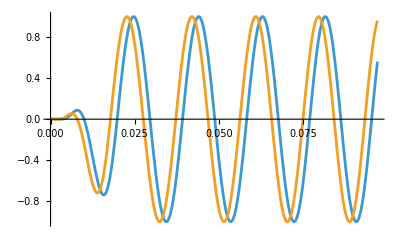
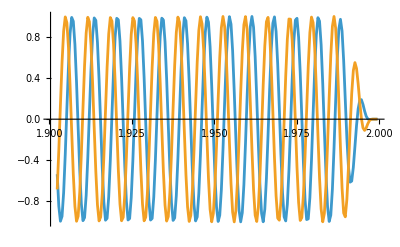

```mathematica
(* Plot the beginning and the end of the two waveforms with the tapers*)
{ListPlot[{Transpose[{tVals2,h1}][[1;;200]],Transpose[{tVals2,h2}][[1;;200]]}, Joined->True],ListPlot[{Transpose[{tVals2,h1}][[-200;;-1]],Transpose[{tVals2,h2}][[-200;;-1]]}, Joined->True]}
```

```mathematica
nTime
```

4096

```mathematica
h1//Length
```

5000

```mathematica
tVals//Length
```

4096

```mathematica
?PadLeft
```

### 2. Build a flat PSD (whitened data)

```mathematica
nFreq=Floor[nTime/2]+1;
psdFlat=FlatPSD[nFreq,deltaF,fLow];
```

### 3. Basic overlap (no time/phase maximization)

```mathematica
(*FFT the tapered waveforms*)
h1Tilde=GWMMatch`Private`ForwardFFT[h1,deltaT];
h2Tilde=GWMMatch`Private`ForwardFFT[h2,deltaT];

overlap=GWOverlap[h1Tilde,h2Tilde,psdFlat,deltaF,fLow,fHigh];
Print["\n-- GWOverlap (no maximization) --"];
Print["Overlap = ",N[overlap,6]];
Print["(Expected: << 1 because of the time shift)"];
```

-- GWOverlap (no maximization) --

Overlap = 0.287329

(Expected: << 1 because of the time shift)

### 4. Discrete match (maximized over time and phase)

```mathematica
{matchDiscrete,peakIndex}=GWMatch[h1,h2,deltaT,psdFlat,deltaF,fLow,fHigh];
recoveredShift=(Length[h1]-peakIndex)*deltaT;  (*seconds*)

Print["\n-- GWMatch (discrete) --"];
Print["Match       = ",N[matchDiscrete,6]];
Print["Peak index  = ",N[peakIndex,8]];
Print["Recovered time shift = ",N[recoveredShift*1000,6]," ms  (true: ",dtShift*1000," ms)"];
```

-- GWMatch (discrete) --

Match       = 0.999776

Peak index  = 4092.91

Recovered time shift = 1.50677 ms  (true: 2. ms)

### 5. Optimized match (sub-sample accuracy via Brent’s method)

```mathematica
{matchOpt,peakIndexOpt}=GWOptimizedMatch[h1,h2,deltaT,psdFlat,deltaF,fLow,fHigh];
recoveredShiftOpt=(Length[h1]-peakIndexOpt)*deltaT;

Print["\n-- GWOptimizedMatch (Brent sub-sample refinement) --"];
Print["Match       = ",N[matchOpt,6]];
Print["Peak index  = ",N[peakIndexOpt,8]];
Print["Recovered time shift = ",N[recoveredShiftOpt*1000,6]," ms  (true: ",dtShift*1000," ms)"];
```

-- GWOptimizedMatch (Brent sub-sample refinement) --

Match       = 0.999776

Peak index  = 4091.91

Recovered time shift = 1.99504 ms  (true: 2. ms)

### 6. Mismatch

```mathematica
GWMismatch[h1,h2,deltaT,psdFlat,deltaF,fLow,fHigh]
```

```mathematica
{0.0002242162943617565,4091.914156227199}
```

{0.000224216,4091.91}

```mathematica
mm=GWMismatch[h1,h2,deltaT,psdFlat,deltaF,fLow,fHigh][[1]];
Print["\n-- GWMismatch --"];
Print["Mismatch = ",ScientificForm[mm],"  (= 1 - match)"];
```

-- GWMismatch --

Mismatch = 2.24216×10^-4  (= 1 - match)

### 7. Repeat with a realistic aLIGO PSD

```mathematica
psdALIGO=DetectorPSD["aLIGOZeroDetHighPower",nFreq,deltaF,fLow];

matchALIGO=GWOptimizedMatch[h1,h2,deltaT,psdALIGO,deltaF,fLow,fHigh][[1]];
Print["\n-- GWOptimizedMatch with aLIGO PSD --"];
Print["Match = ",N[matchALIGO,6]];
Print["Mismatch = ",ScientificForm[1-matchALIGO]];
```

-- GWOptimizedMatch with aLIGO PSD --

Match = 0.999751

Mismatch = 2.4856×10^-4

### 8. Self-match sanity check

```mathematica
selfMatch=GWOptimizedMatch[h1,h1,deltaT,psdALIGO,deltaF,fLow,fHigh][[1]];
Print["\n-- Self-match sanity check --"];
Print["match(h1, h1) = ",N[selfMatch,10],"  (should be 1.0)"];
```

-- Self-match sanity check --

match(h1, h1) = 1.  (should be 1.0)